```mathematica
LaunchKernels[10]
```

{Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10)}

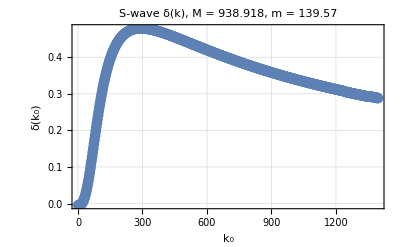

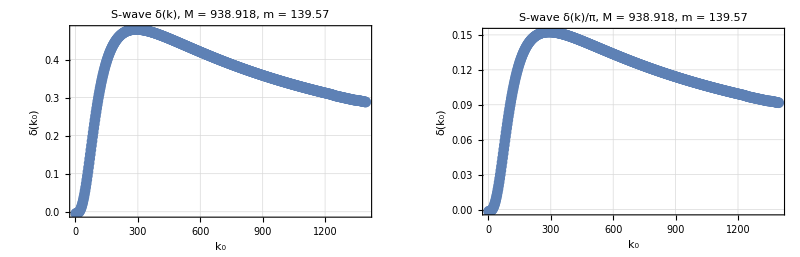

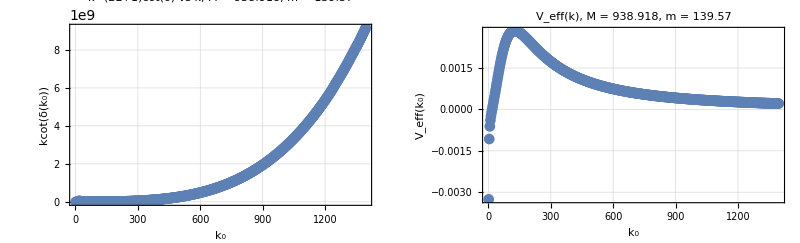

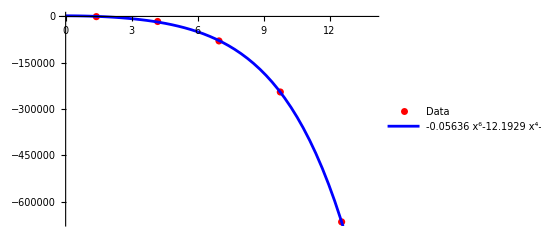

```mathematica
(*---PARAMETERS---*)
M=938.918;                (* Mass of Nucleon M=938.918*)
m=139.570;             (*Pion mass m=139.570*)
(*α=0.128351*M;               (*Depth of Yukawa potential, 0.128351*)
gA = Sqrt[4Pi*α/M]; (*Axial coupling, experimentally 1.27*)
fπ=132;                         (*Pion decay constant*)*)

gA=1.25;
fπ=130.2;
α=(gA^2m^2/(8Pi*fπ^2))*M; (* The extra factor of 1/4Pi which doesnt seem to appear in the expression for V(q) comes essentially from the fourier transform, or really how the amplitude is related to the potention in the first born approximation. It seems in the literature this extra factor of 1/4Pi is absorbed into the defintion of V(q) such that A=-V(q) instead of somethinglike A=-1/(4Pi) V(q)*)

r0=10^-6;          (*Small value near r=0 for boundary condition*)
l=1;
channelfactor = 6; (* overall potential factor due to spin and isospin contractions*)

kMin = m/100;
kMax =10*m; 
kSpacing = (kMax-kMin)/500(*0.01*m^2*);
λ = 2*Pi/Abs[m]; (* De Broglie Wavelength*)
rMax=10*λ;           (*Max radius for numerical integration, ensures asymptotic behavior by being much larger than λ*)
fitStart=0.8*rMax;       (*Start of asymptotic region*)
fitEnd=rMax;         (*End of asymptotic region*)
fitSpacing = rMax/100;    (* Interval spacing in asymptotic region*)

(*---Yukawa Potential*2μ---*)
V[r_]:=-channelfactor *α*Exp[-m*r]/r+l(l+1)/(r^2);

ccsol[k_,g_]={cc[2]->-g/(1+L),cc[3]->(3 g^2)/(2 (1+L))-(3 ((-1+g) g+k^2))/(3+2 L),cc[4]->-(g (g^2+2 (1+L) (3+2 L)-2 k^2 (4+3 L)+g (8+6 L)))/((1+L) (2+L) (3+2 L)),cc[5]->(5 (g^4+12 k^4 (1+L) (2+L)-4 g (-3+6 k^2-2 L) (1+L) (2+L)+4 g^3 (5+3 L)+g^2 (66-4 k^2 (5+3 L)+4 L (22+7 L))))/(4 (1+L) (2+L) (3+2 L) (5+2 L)),cc[6]->(3 g (-g^4-20 g^3 (2+L)-4 (1+L) (2+L) (3+2 L) (5+2 L)+8 k^2 (1+L) (5+2 L) (9+5 L)-4 k^4 (46+5 L (11+3 L))+2 g^2 (-173+10 k^2 (2+L)-10 L (19+5 L))+4 g (-156+2 k^2 (46+5 L (11+3 L))-L (283+L (163+30 L)))))/(4 (1+L) (2+L) (3+L) (3+2 L) (5+2 L)),cc[7]->(7 (g^6-120 k^6 (1+L) (2+L) (3+L)+10 g^5 (7+3 L)+8 g (1+L) (2+L) (3+L) (45 k^4+(3+2 L) (5+2 L)-5 k^2 (13+6 L))+2 g^4 (623-5 k^2 (7+3 L)+10 L (58+13 L))+4 g^3 (1551-2 k^2 (196+15 L (13+3 L))+L (2368+L (1153+180 L)))+4 g^2 (k^4 (196+15 L (13+3 L))-k^2 (1545+L (2551+2 L (653+105 L)))+2 (855+L (1901+L (1508+L (509+62 L)))))))/(8 (1+L) (2+L) (3+L) (3+2 L) (5+2 L) (7+2 L))};
u0[L_,r_] =r^L( r + Sum[cc[n] r^n/n! ,{n,2,7}]);
uinit[L_,r_,k_,g_] = u0[L,r]/.ccsol[k,g];
Duinit[L_,r_,k_,g_] = D[u0[L,r],r]/.ccsol[k,g];

(*---Phase Shift Extractor---*)
ClearAll[extractPhaseShift]

extractPhaseShift2[k0_?Positive,rm_?Positive]:=Module[{k,sol,uFunc,data,fit,δ},k=k0;
(*Numerical solution to Schrödinger equation*)

Quiet[sol=NDSolve[{u''[r]==(V[r]-k0^2) u[r],u[r0]==uinit[l,r0,k0,α],u'[r0]==Duinit[l,r0,k0,α]},u,{r,r0,rm},MaxSteps->Infinity,WorkingPrecision->30],NDSolve::precw]; (*MaxSteps->10^5,AccuracyGoal->Automatic,PrecisionGoal->50,WorkingPrecision->MachinePrecision*)
(*Wavefunction interpolator*)uFunc=Function[r,Evaluate[u[r]/. sol[[1]]]];
waveLast[r_?NumericQ]:=uFunc[r];
(*Sample numerical wavefunction in asymptotic region*)(*data=Table[{r,uFunc[r]},{r,0.8*rm,rm,rm/100}];*)
vals=Table[uFunc[r],{r,0.8*rm,rm,rm/100}];
maxVal=Max[Abs[vals]];
data=Table[{r,uFunc[r]/maxVal},{r,0.8*rm,rm,rm/100}];
(*Fit to A*Sin[k*r+δ] to extract phase shift*)fit=NonlinearModelFit[data,A*Sin[k*r-l*Pi/2+δ],{{A,1},{δ,0}},r,MaxIterations->∞]; (*MaxIterations->∞*)
fitLast=fit;
(*Return δ modulo π (optional,depending on context)*)Mod[δ/. fit["BestFitParameters"],Pi](*δ/.fit["BestFitParameters"]*)]

(*extractPhaseShift3[k0_?Positive,rm_?Positive]:=Module[{sol,uFunc,ul,dul,jl,nl,jlp,nlp,tanδ},(*---integrate---*)Quiet[sol=NDSolve[{u''[r]==(V[r]-k0^2) u[r],u[r0]==uinit[l,r0,k0,α],u'[r0]==Duinit[l,r0,k0,α]},u,{r,r0,rm},MaxSteps->Infinity,WorkingPrecision->30][[1]],NDSolve::precw];
uFunc[r_]=Evaluate[u[r]/. sol];
(*---pick a single point in the asymptotic region---*)ul=uFunc[rm];
dul=D[uFunc[r],r]/. r->rm;
jl=SphericalBesselJ[l,k0 rm];
nl=SphericalBesselY[l,k0 rm];
jlp=D[SphericalBesselJ[l,x],x]/. x->k0 rm;
nlp=D[SphericalBesselY[l,x],x]/. x->k0 rm;
(*algebraic formula:tan δ₁=(…)*)tanδ=(k0 jlp-dul/ul jl)/(k0 nlp-dul/ul nl);
     ArcTan[tanδ]                        (*gives δ₁ in (-π/2,π/2)*)]*)

extractPhaseShift1[k0_?Positive,rm_?Positive]:=Module[{sol,uFunc,(*integration stuff*)tanDeltaAt,rs,tol=10^-8,(*averaging stuff*)goodTan,δavg},(*---integrate Schrödinger eqn (unchanged)-----------------------*)Quiet[sol=NDSolve[{u''[r]==(V[r]-k0^2) u[r],u[r0]==uinit[l,r0,k0,α],u'[r0]==Duinit[l,r0,k0,α]},u,{r,r0,rm},MaxSteps->Infinity,WorkingPrecision->30][[1]],NDSolve::precw];
uFunc[r_]=Evaluate[u[r]/. sol];
(*---single-point formula wrapped as a function of r-------------*)tanDeltaAt[r_?NumericQ]:=Module[{ul=uFunc[r],dul=uFunc'[r],jl,nl,jlp,nlp},jl=SphericalBesselJ[l,k0 r];
nl=SphericalBesselY[l,k0 r];
jlp=D[SphericalBesselJ[l,x],x]/. x->k0 r;
nlp=D[SphericalBesselY[l,x],x]/. x->k0 r;
(k0 jlp-(dul/ul) jl)/(k0 nlp-(dul/ul) nl)];
(*---sample many radii,skip nodes,average----------------------*)rs=Subdivide[0.8 rm,rm,40]; (*40 points*)
goodTan=tanDeltaAt/@Select[rs,Abs[uFunc[#]]>tol&];
δavg=Mean[ArcTan[goodTan]];(*(-π/2,π/2)*)
δavg(*return phase shift*)]
extractPhaseShift3[k0_?Positive,rm_?Positive]:=Module[{sol,uFunc,(*integration stuff*)tanDeltaAt,rs,tol=10^-8,(*averaging stuff*)goodTan,δavg},(*---integrate Schrödinger eqn (unchanged)-----------------------*)Quiet[sol=NDSolve[{u''[r]==(V[r]-k0^2) u[r],u[r0]==uinit[l,r0,k0,α],u'[r0]==Duinit[l,r0,k0,α]},u,{r,r0,rm},MaxSteps->Infinity,WorkingPrecision->30][[1]],NDSolve::precw];
uFunc[r_]=Evaluate[u[r]/. sol];
(*---single-point formula wrapped as a function of r-------------*)tanDeltaAt[r_?NumericQ]:=Module[{ul=uFunc[r],dul=uFunc'[r],jl,nl,jlp,nlp},jl=SphericalBesselJ[l,k0 r];
nl=SphericalBesselY[l,k0 r];
jlp=D[SphericalBesselJ[l,x],x]/. x->k0 r;
nlp=D[SphericalBesselY[l,x],x]/. x->k0 r;
{(k0 jlp-(dul/ul) jl),(k0 nlp-(dul/ul) nl)}];
(*---sample many radii,skip nodes,average----------------------*)rs=Subdivide[0.8 rm,rm,40]; (*40 points*)
goodTan=tanDeltaAt/@Select[rs,Abs[uFunc[#]]>tol&];
δavg=Mean[ArcTan[goodTan[[2]],goodTan[[1]]]];(*(-π/2,π/2)*)
δavg(*return phase shift*)]




(*extractPhaseShift2[k0_?Positive,rm_?Positive]:=Module[{k,sol,uFunc,data,fit,δ},k=k0;
(*Numerical solution to Schrödinger equation*)sol=NDSolve[{u''[r]==(V[r]-k0^2) u[r],u[r0]==r0^(l+1),u'[r0]==1},u,{r,r0,rm},MaxSteps->Infinity];
(*Wavefunction interpolator*)uFunc=Function[r,Evaluate[u[r]/. sol[[1]]]];
(*Sample numerical wavefunction in asymptotic region*)data=Table[{r,uFunc[r]},{r,0.8*rm,rm,rm/100}];
(*Fit to A*Sin[k*r+δ] to extract phase shift*)fit=NonlinearModelFit[data,A*Sin[k*r-l*Pi/2+δ],{{A,1},{δ,0}},r,MaxIterations->∞]; (*MaxIterations->∞*)
(*Return δ modulo π (optional,depending on context)*)Mod[δ/. fit["BestFitParameters"],Pi](*δ/.fit["BestFitParameters"]*)]*)

(*---Phase Shift Curve Generator---*)
kRange=Range[kMin,kMax,kSpacing];  (*k's to test*)
rMaxList =(20*(2 Pi/#))&/@kRange;
pairs = Transpose[{kRange,rMaxList}];

(* ---Loop through the values of k_n and rmax_n to construct the data--- *)
phaseShiftData1=ParallelTable[{kRange[[i]],extractPhaseShift1[kRange[[i]],rMaxList[[i]]](*-extractPhaseShift1[kRange[[1]],rMaxList[[1]]]*)},{i,Length[kRange]}]; 

(*(* --- test to see solution to Schrodinger eqn and how it matches the fit*)
test = 2;
kRange[[test]];
rMaxtest = rMaxList[[test]];
rMaxtest = 10*(2Pi/kRange[[test]]);
extractPhaseShift1[kRange[[test]],rMaxtest];

params=fitLast["BestFitParameters"];
phaseShiftData1[[test]];
AVal=params[[1,2]];
δVal=params[[2,2]];

GraphicsGrid[{{Plot[waveLast[r]/maxVal,{r,0.8*rMaxtest,rMaxtest}],Plot[Evaluate[AVal*Sin[kRange[[test]]*r-l*Pi/2+δVal]/. fitLast["BestFitParameters"]],{r,0.8 rMaxtest,rMaxtest}]}},ImageSize->800]*)


(* ---Make the phases continuous by gluing together the pieces--- *)
unwrapPhaseReverse[data_]:=Module[{ks,deltas,unwrapped,shifts,jumpIndices},{ks,deltas}=Transpose[data];
unwrapped=deltas;
Do[If[unwrapped[[i]]-unwrapped[[i-1]]>Pi/2,(*Apply+π to all previous values*)unwrapped[[1;;i-1]]+=Pi;],{i,2,Length[unwrapped]}];
Transpose[{ks,unwrapped}]];

phaseShiftData1Unwrapped=unwrapPhaseReverse[phaseShiftData1];

(*---Plot the phase shift vs k---*)
dplot = ListPlot[phaseShiftData1,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave δ(k), M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None]
dplotstitched = ListPlot[{#[[1]],#[[2]]/Pi}&/@phaseShiftData1Unwrapped,PlotMarkers->Automatic,AxesLabel->{"k₀","δ(k₀)"},PlotLabel->Row[{"S-wave δ(k)/π, M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None];

GraphicsGrid[{{dplot,dplotstitched}},ImageSize->800]

kmax=m/10;
kcotd = {#[[1]],(#[[1]])^(2l+1)*Cot[#[[2]]]}&/@phaseShiftData1Unwrapped;
veff = {#[[1]],1/(#[[1]]*Cot[#[[2]]])}&/@phaseShiftData1Unwrapped;
kcotdlowk=Select[kcotd,#[[1]]<=kmax&];
vefflowk = Select[veff,#[[1]]<=kmax&];
cotdrootIm= {#[[1]],Cot[#[[2]]]}&/@phaseShiftData1Unwrapped;
(*scatlen= {#[[1]],-#[[2]]}&/@phaseShiftData1Unwrapped;-del[0,V0,0.001]/0.001*)

kcotdfit = Fit[kcotd,{x^(2l),x^(2l+2),x^(2l+4)},x];
kcotdfitlowk4= Fit[kcotdlowk,{x^(2l-2),x^(2l),x^(2l+2),x^(2l+4)},x];
kcotdfitlowk2=Normal[Series[kcotdfitlowk4,{x,2l,2l+2}]];


kcotdplot = ListPlot[kcotd,PlotMarkers->Automatic,AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"k^(2L+1)cot(δ) vs k, M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None];
veffplot = ListPlot[veff,PlotMarkers->Automatic,AxesLabel->{"k₀","V_eff(k₀)"},PlotLabel->Row[{"V_eff(k), M = ",M,", m = ",m}],Frame->True,GridLines->Automatic,PlotRange->{Automatic,All},PerformanceGoal->"Speed",PlotMarkers->None];

GraphicsGrid[{{kcotdplot,veffplot}},ImageSize->800]

kcotdlowkplot = Show[ListPlot[kcotdlowk,PlotStyle->Red,PlotLegends->{"Data"}, PlotRange->{{0,kmax},Automatic},PerformanceGoal->"Speed",PlotMarkers->None],Plot[kcotdfitlowk4,{x,0,kmax},PlotStyle->Blue,PlotLegends->{ToString[TraditionalForm[kcotdfitlowk4]]}]]
```

{{x→-1.41666-0.000462941 ⅈ},{x→0.539354+7.97763 ⅈ},{x→0.539406-7.97666 ⅈ},{x→1.4959-0.00051088 ⅈ}}

InterpolatingFunction::dmval: Input value {-350.188} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.270998} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-350.187862029103675294331070489} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.27099826205958954109745835056} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

1.24049698755293184706813015796

InterpolatingFunction::dmval: Input value {1.24049698755293184706813015796} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

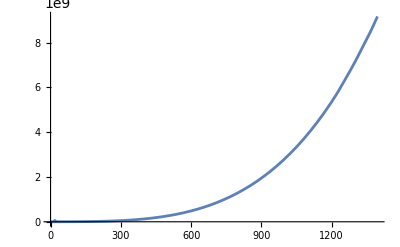

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

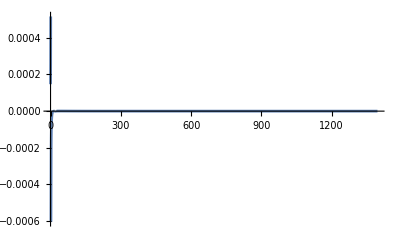

```mathematica
Solve[kcotdfitlowk2-I*x==0]
kcotdInterp = Interpolation[kcotd];
(* Define function an left and right of the pole so that it doesnt smooth over pole structure*)
veffInterp[k_]=1/kcotdInterp[k];
kp1= x/.FindRoot[kcotdInterp[x]==0,{x,100}];
kp=x/. FindRoot[kcotdInterp[x]==0,{x,100},WorkingPrecision->30,AccuracyGoal->20]


kcotdInterpprime=kcotdInterp';
residue=1/kcotdInterpprime[kp];

(*Double checking residue makes sense*)(* IT DOESNT RIGHT NOW, USE FIRST DEF*)
(* Define function an left and right of the pole so that it doesnt smooth over pole structure*)
(*kcotdInterpleft1=Interpolation[Select[kcotd,First[#]<=kp+0.05&]];
kcotdInterpright1=Interpolation[Select[kcotd,First[#]>=kp-0.05&]];
veffInterpleft1[x_]:=1/kcotdInterpleft1[x];
veffInterpright1[x_]:=1/kcotdInterpright1[x];
resLeft=(kp-10^(-11)-kp)*veffInterpleft1[kp-10^(-11)];
resRight=(kp+10^(-11)-kp)*veffInterpright1[kp+10^(-11)];
residue1=N[(resLeft+resRight)/2];
kcotdInterpleft1["Domain"];
kcotdInterpright1["Domain"];*)
(*---*)

kr=residue;

y=Sqrt[2*kr*kp/M];
Δ=kp^2/M;
Plot[kcotdInterp[x],{x,0,kMax},PlotRange->All]
Plot[veffInterp[x],{x,0,kMax},PlotRange->All]
(*Res[zr_]:=2*zr*(z-zr)*V[z]/.{z->zr+10^(-11)};*)
```

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

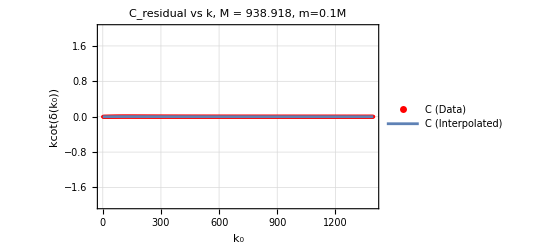

-0.00134394

-0.00134394+0.000246849 (-2.7914+k1)-0.00001772 (-2.7914+k1)^2

-0.00134394+0.000246849 (-2.7914+k1)-0.00001772 (-2.7914+k1)^2+3.00736×10^-7 (-2.7914+k1)^3

-0.00134394+0.000246849 (-2.7914+k1)-0.00001772 (-2.7914+k1)^2+3.00736×10^-7 (-2.7914+k1)^3

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

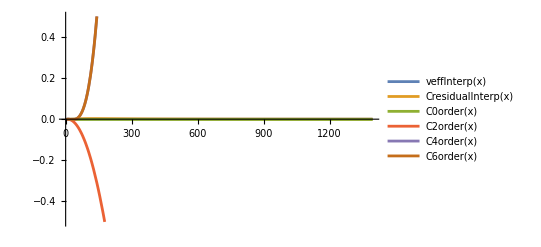

InterpolatingFunction::dmval: Input value {0.0000278757} lies outside the range of data in the interpolating function. Extrapolation will be used.

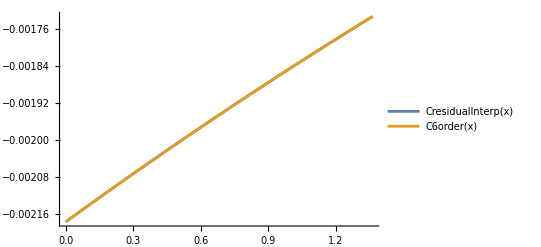

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

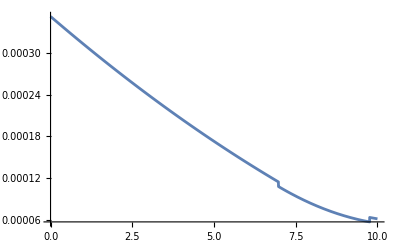

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

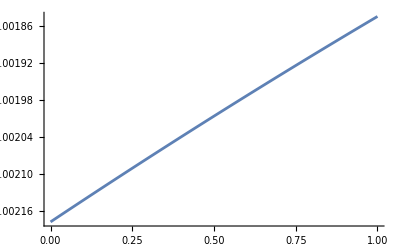

```mathematica
Cresidual = {#[[1]],#[[2]]-y^2/(#[[1]]^2/M-Δ)}&/@veff;
CresidualInterp = Interpolation[Cresidual];
Show[ListPlot[Cresidual,PlotStyle->{Red,PointSize[0.007]},AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"C_residual vs k, M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,{-2,2}},PlotLegends->{"C (Data)"}],
Plot[CresidualInterp[x],{x,0,kMax},PlotStyle->{PointSize[0.007]},AxesLabel->{"k₀","kcot(δ(k₀))"},PlotLabel->Row[{"C_residual (interpolated) vs k, M = ",M,", m=0.1M"}],Frame->True,GridLines->Automatic,PlotTheme->"Detailed",PlotRange->{Automatic,{-2,2}},PlotLegends->{"C (Interpolated)"}]]

(*Cresidualtaylor1[k0_,n_]:=Module[{taylorTerms,k},taylorTerms=Table[Derivative[m][CresidualInterp][k0]/m!*(k-k0)^m,{m,0,n}];
Total[taylorTerms]];
CresidualTaylor[k0_?NumericQ,n_Integer?NonNegative]:=Function[k,Sum[Derivative[m][CresidualInterp][k0]/Factorial[m]*(k-k0)^m,{m,0,n}]];
C0=CresidualTaylor[1,0];
C2=CresidualTaylor[1,2];
C4=CresidualTaylor[1,4];
C6=CresidualTaylor[1,6];*)

k0=2*kMin;

f0=CresidualInterp[k0];
f1=Derivative[1][CresidualInterp][k0];
f2=Derivative[2][CresidualInterp][k0];
f3=Derivative[3][CresidualInterp][k0];
f4=Derivative[4][CresidualInterp][k0];
f5=Derivative[5][CresidualInterp][k0];
f6=Derivative[6][CresidualInterp][k0];

C0order[k1_]=f0
C2order[k1_]=f0+f1*(k1-k0)+f2/2*(k1-k0)^2
C4order[k1_]=f0+f1*(k1-k0)+f2/2*(k1-k0)^2+f3/6*(k1-k0)^3+f4/24*(k1-k0)^4
C6order[k1_]=f0+f1*(k1-k0)+f2/2*(k1-k0)^2+f3/6*(k1-k0)^3+f4/24*(k1-k0)^4+f5/120*(k1-k0)^5+f6/720*(k1-k0)^6


Plot[{veffInterp[x],CresidualInterp[x],C0order[x],C2order[x],C4order[x],C6order[x]},{x,0,kMax},PlotRange->{Automatic,{-0.5,0.5}},PlotLegends->"Expressions"]
Plot[{CresidualInterp[x],C6order[x]},{x,0,1.1*kp},PlotLegends->"Expressions"]
Plot[D[CresidualInterp[s],{s,1}]/.{s->x},{x,0,10}]
Plot[CresidualInterp[x],{x,0,1},PlotLegends->"Expressions"]
```

1/k^6((3.84141×10^12+7.888×10^8 k^2+40493.2 k^4) Im[PolyLog[2,((0.+0.00716486 ⅈ)-0.000102671 k) k]]+(3.84141×10^12+7.888×10^8 k^2+40493.2 k^4) Im[PolyLog[2,(0.5 k)/((0.+69.785 ⅈ)+1. k)]]+k (((0.-7.27596×10^-12 ⅈ)-201.229 k) k^3+k (-7.888×10^8-80986.5 k^2) ArcTan[(69.785 k)/(9739.89+k^2)]+5.50464×10^10 Log[1+0.0000513353 k^2])+k^2 ((0.+5.96046×10^-8 ⅈ)+k (979976.+k ((0.+5.45697×10^-12 ⅈ)+100.615 k))) Log[1+0.000205341 k^2]+((4.06576×10^-20-0.000244141 ⅈ)+k (-4.23516×10^-22+(9.92617×10^-24-2.98023×10^-8 ⅈ) k+(4.03897×10^-28-1.81899×10^-12 ⅈ) k^3)) Log[1+0.000205341 k^2]^2)

1/k^6((3.84141×10^12+7.888×10^8 k^2+40493.2 k^4) Im[PolyLog[2,((0.+0.00716486 ⅈ)-0.000102671 k) k]]+(3.84141×10^12+7.888×10^8 k^2+40493.2 k^4) Im[PolyLog[2,(0.5 k)/((0.+69.785 ⅈ)+1. k)]]+k (((0.-7.27596×10^-12 ⅈ)-201.229 k) k^3+k (-7.888×10^8-80986.5 k^2) ArcTan[(69.785 k)/(9739.89+k^2)]+5.50464×10^10 Log[1+0.0000513353 k^2])+k^2 ((0.+5.96046×10^-8 ⅈ)+k (979976.+k ((0.+5.45697×10^-12 ⅈ)+100.615 k))) Log[1+0.000205341 k^2]+((4.06576×10^-20-0.000244141 ⅈ)+k (-4.23516×10^-22+(9.92617×10^-24-2.98023×10^-8 ⅈ) k+(4.03897×10^-28-1.81899×10^-12 ⅈ) k^3)) Log[1+0.000205341 k^2]^2)

1.07462×10^-6+1.28318×10^-11 ⅈ

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

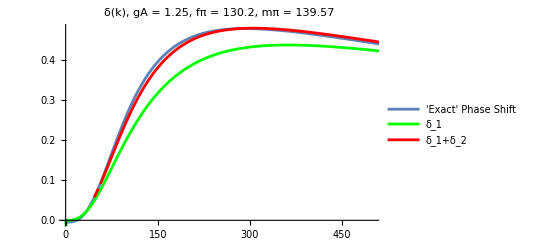

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

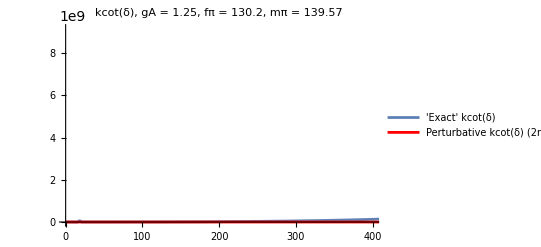

InterpolatingFunction::dmval: Input value {0.0285122} lies outside the range of data in the interpolating function. Extrapolation will be used.

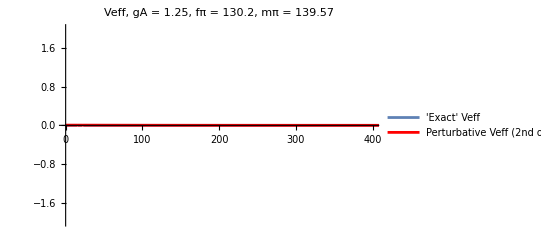

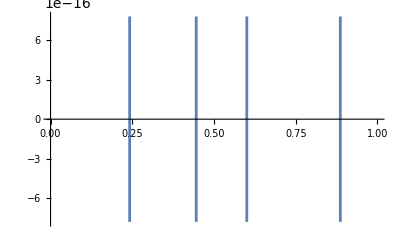

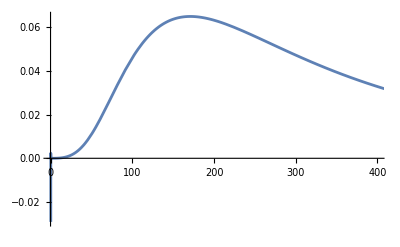

-Graphics-

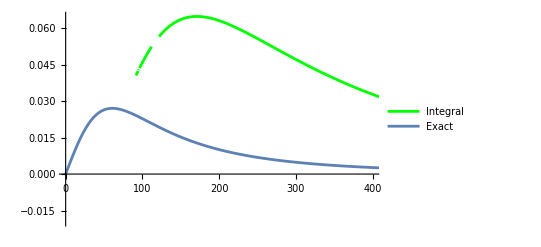

```mathematica
(*C01S0 = -3.34*(2.568×10^−5); (*fm^2 = 2.568×10^−5 MeV^-2,  -3.63 fm^2, −3.34 fm^2*)
C21S0 = 3.24*(2.568×10^−5)^2; (*2.92 fm^4, 3.24 fm^4 *)
D21S0 = -0.42*(2.568×10^−5)^2; (*0, -0.42*)

Am1[k_] = -C01S0/(1+C01S0*M/(4Pi)(μ+I*k));
A01[k_]=-C21S0*k^2*(Am1[k]/C01S0)^2;
A02[k_]=gA^2/(2fπ^2)(-1+m^2/(4k^2)Log[1+4k^2/m^2]);
A03[k_]=gA^2/fπ^2(m*M*Am1[k]/(4Pi))(-(μ+I*k)/m+m/(2k)(ArcTan[2k/m]+I/2Log[1+4k^2/m^2]));
A04[k_]=gA^2/(2fπ^2)(m*M*Am1[k]/(4Pi))^2(-((μ+I*k)/m)^2+(I*ArcTan[2k/m]-1/2Log[(m^2+4k^2)/μ^2]+1));
A05[k_]=-D21S0*m^2(Am1[k]/C01S0)^2;
A0[k_]=A01[k]+A02[k]+A03[k]+A04[k]+A05[k];*)

(*A12Pi[k_]=(I*M/(4Pi)(gA^2/(2fπ^2))^(2))((*I*k-I*m^2/k Log[1-2I*k/m]*)+m^4/(4k^3)(I/4 (Log[1+4k^2/m])^2+Im[PolyLog[2,(2k^2-I*k*m)/(m^2+4k^2)]]+Im[PolyLog[2,(-2k^2+I*k*m)/m^2]]))*)

(*delta0[k_]=1/(2I)Log[1+I*M*k/(2Pi)Am1[k]];
delta1[k_]=M*k/(4Pi)(A0[k]/(1+I*M*k/(2Pi)Am1[k]));
deltatot[k_]=delta0[k]+delta1[k];*)

A02Pinocontact[k_]=gA^2/(2fπ^2)(m^2/(4k^2)Log[1+4k^2/m^2]);

A02PinocontactP[k_]=channelfactor*gA^2/(4fπ^2)((m^4/(4k^4)+m^2/(2k^2))Log[1+4k^2/m^2]-m^2/k^2);
(*A02PinocontactP[0]=Limit[channelfactor*gA^2/(4fπ^2)((m^4/(4k^4)+m^2/(2k^2))Log[1+4k^2/m^2]-m^2/k^2),k->0] (*Have to do this to fix behavior at origin to graph properly*)*)
(*A02PinocontactP[k_]=gA^2/fπ^2 (k^2/m^2-4 k^4/m^4+72 k^6/(5 m^6)-256 k^8/(5 m^8));*)
(*A02PinocontactP[k_]=3gA^2/(4fπ^2)((m^4/(24k^4))Log[1+4k^2/m^2]-m^2/(6k^2))*)

A12Pinocontact[k_]=(M/(4Pi)(gA^2/(2fπ^2))^(2))(m^4/(4k^3)(I/4 (Log[1+4k^2/m^2])^2+Im[PolyLog[2,(2k^2-I*k*m)/(m^2+4k^2)]]+Im[PolyLog[2,(-2k^2+I*k*m)/m^2]]));

(*A12PinocontactP[k_?NumericQ] :=1/(2k^2) * (2M^2(gA^2m^2/(8Pi*fπ^2))^2) NIntegrate[ (1-q^2/(2k^2))*(1/(Sqrt[α^4+4α^2k^2+k^2q^2])) * (2ArcTan[m*q/(2Sqrt[α^4+4α^2k^2+k^2q^2])]),{q,0,2k}];*)
(*A12PinocontactP1[k_?NumericQ] :=1/2 * (2M^2(gA^2m^2/(8Pi*fπ^2))^2) NIntegrate[ (*x**)(1/((k*Sqrt[2-2x])*Sqrt[(α/M)^4+4(α/M)^2k^2+k^2(2k^2*(1-x))])) * (2ArcTan[m*(k*Sqrt[2-2x])/(2Sqrt[(α/M)^4+4(α/M)^2k^2+k^2(2k^2*(1-x))])]),{x,-1,1}];*)
(*A12PinocontactP[p_?NumericQ]:=(M*m^4/2)*(gA^2/(2fπ^2))^2NIntegrate[Module[{x,qVec,k,th,phi,kVec,kDotP,kMinusQ2,denom,measure},(*outer weight*)x=cosθ;
(*q vector as function of x*)qVec={p Sqrt[1-x^2],0,p (x-1)};
(*spherical k-vector*)kVec=k {Sin[th] Cos[phi],Sin[th] Sin[phi],Cos[th]};
(*dot products*)kDotP=kVec.{0,0,p};(* =k p Cos[θ_k]*)kMinusQ2=(kVec-qVec).(kVec-qVec);
(*denominator*)denom=(k^2+2 kDotP) (k^2+m^2) (kMinusQ2+m^2);
(*measure d^3k=k^2 sinθ_k dk dθ_k dφ,and p-wave weight x*)measure=x*k^2*Sin[th];
(*full integrand including (2π)^(-3)*)measure/(denom (2 π)^3)],(*integrals:cosθ,then k,θ_k,φ*){cosθ,-1,1},{k,0,kMax},{th,0,π},{phi,0,2 π},Method->"QuasiMonteCarlo",PrecisionGoal->3]*)
A12PinocontactP[k_]=channelfactor^2((M/(4Pi)(gA^2/(2fπ^2))^(2))(m^4/(4k^3)(I/4 (Log[1+4k^2/m^2])^2+Im[PolyLog[2,(2k^2-I*k*m)/(m^2+4k^2)]]+Im[PolyLog[2,(-2k^2+I*k*m)/m^2]]))-(M/(4Pi)(gA^2/(2fπ^2))^(2))(m^4/(4k^3))(((m^2+2k^2)/k^2)ArcTan[m k/(m^2+2k^2)]-m^3/(2k^3)Log[1+k^2/m^2]-(m^2/k^2+m^4/(4k^4))(Im[PolyLog[2,(2k^2-I*k*m)/(m^2+4k^2)]]+Im[PolyLog[2,(-2k^2+I*k*m)/m^2]])-I+I(1+m^2/(2k^2))Log[1+4k^2/m^2]-I/4(m^2/k^2+m^4/(4k^4))(Log[1+4k^2/m^2])^2));


delta1justpion[k_]=M*k*(A02Pinocontact[k])/(4Pi);
delta2justpion[k_]=k*M/(4Pi)A12Pinocontact[k]-I((k*M)/(4Pi))^2(A02Pinocontact[k])^2;
deltajustpion[k_]=FullSimplify[delta1justpion[k]+delta2justpion[k]];

delta1justpionP[k_]=M*k*(A02PinocontactP[k])/(4Pi);
delta2justpionP[k_]=k*M/(4Pi)A12PinocontactP[k]-I((k*M)/(4Pi))^2(A02PinocontactP[k])^2;
deltajustpionP[k_]=FullSimplify[delta1justpionP[k]+delta2justpionP[k]];
deltajustpionP[k]

(*Clear[m,M,gA,fπ]*)
deltajustpionPtest = deltajustpionP[k] /. {M->Symbol["M"],m->Symbol["m"],gA->Symbol["gA"],fπ->Symbol["fπ"]};
FullSimplify[deltajustpionPtest]
deltajustpionP[1]


dplotstitchedinterp = Interpolation[{#[[1]],#[[2]]}&/@phaseShiftData1Unwrapped];
dplotstitchedinterppoleremoved[k_]= ArcCot[1/(k*CresidualInterp[k])];

Show[Plot[dplotstitchedinterp[x],{x,0,kMax},PlotLegends->{"'Exact' Phase Shift"},PlotRange->{{0,500},Automatic}],(*Plot[dplotstitchedinterppoleremoved[x],{x,0,kMax},PlotLegends->{"'Exact' Phase Shift (pole removed)"},PlotRange->{{0,500},All},PlotStyle->Magenta],*)Plot[(delta1justpionP[x]),{x,0,kMax},PlotStyle->Green,PlotLegends->{"δ_1"},PlotRange->{{1,500},{-0.5,0.5}}],Plot[(deltajustpionP[x]),{x,0,kMax},PlotStyle->Red,PlotLegends->{"δ_1+δ_2"},PlotRange->{{1,500},{-0.5,0.5}}],PlotLabel->Row[{"δ(k), gA = ",gA,", fπ = ",fπ, ", mπ = ",m}]]
Show[Plot[kcotdInterp[x],{x,0,kMax},PlotLegends->{"'Exact' kcot(δ)"},PlotRange->{{0,400},Automatic}],Plot[x*Cot[deltajustpion[x]],{x,0,kMax},PlotStyle->Red,PlotLegends->{"Perturbative kcot(δ) (2nd order)"},PlotRange->{{0,400},Automatic}],PlotLabel->Row[{"kcot(δ), gA = ",gA,", fπ = ",fπ, ", mπ = ",m}]]
Show[Plot[1/kcotdInterp[x],{x,0,kMax},PlotLegends->{"'Exact' Veff"},PlotRange->{{0,400},{-2,2}}],Plot[1/(x*Cot[deltajustpion[x]]),{x,0,kMax},PlotStyle->Red,PlotLegends->{"Perturbative Veff (2nd order)"},PlotRange->{{0,400},{-2,2}}],PlotLabel->Row[{"Veff, gA = ",gA,", fπ = ",fπ, ", mπ = ",m}]]
Plot[Im[delta2justpionP[x]],{x,0,500},PlotRange->{{0,1},Automatic}]
Plot[x*M/(4Pi)Re[A12PinocontactP[x]],{x,0,500},PlotRange->{{0,400},Automatic}]
Plot[x*M/(4Pi)Re[A12PinocontactP1[x]],{x,0,500},PlotRange->{{0,400},Automatic}]
Show[Plot[delta2justpionP[x],{x,0,500},PlotRange->{{0,400},Automatic},PlotStyle->Green,PlotLegends->{"Integral"}],
Plot[delta2justpion[x],{x,0,500},PlotRange->{{0,400},Automatic},PlotLegends->{"Exact"}]]
```